```mathematica
(* notebook to manipulate the stringbit numerical results. *)

ClearAll[ResultFolder,LoadEnergyData,LoadTotalEnergy,LoadEvsS];
ResultFolder = NotebookDirectory[]<>"../results/";

LoadTotalEnergy[s_,xi_]:=Module[{file,data},
file = "Es="<> ToString[s] <> "xi="<>ToString[xi];
data = Import[ResultFolder<> file <> ".txt", "Table"];
data=data[[2;;Length[data]]];
Return[data];
];

(*DataSet: 0 for all data point, 1 for odd only, 2 for even only *)
Options[LoadEvsS]={LogData->False,DataSet->0};
LoadEvsS[M_,xi_,opts:OptionsPattern[]]:=Module[{file,data,i,len},
file = "Exi="<> ToString[xi] <> "M="<>ToString[M];
data = Import[ResultFolder<> file <> ".txt", "Table"];
data=data[[2;;Length[data]]];
If[OptionValue[LogData],
For[i=1,i≤ Length[data],i++,
data[[i,2]]=Log10[Abs[data[[i,2]]]];
];
];

If[OptionValue[DataSet]==0, Return[data]];

len = Length[data];
If[OptionValue[DataSet] == 1, 
Return[Table[data[[2*i-1]],{i,1,Floor[(len+1)/2]}]]
];

If[OptionValue[DataSet] == 2,
Return[Table[data[[2*i]],{i,1,Floor[len/2]}]]
];
];


(*DataSet: 0 for all data point, 1 for odd only, 2 for even only, 3 for data[L] + data[M-L] *)
Options[LoadEnergyData]={DataSet->0,NormalizeFactorM->0};
LoadEnergyData[s_,xi_,M_,opts:OptionsPattern[]]:=Module[{file,data,dataType, ret, len,normpower},
file = "s="<>ToString[s]<>"-M="<>ToString[M];
If[xi≠0, file = file <> "-xi="<>ToString[xi]];
data=Import[ResultFolder<>file<>".txt","Table"];

normpower = OptionValue[NormalizeFactorM];
data=data[[2;;Length[data],{2,3}]];
Do[data[[i,1]]=N[data[[i,1]]/M];data[[i,2]]=N[data[[i,2]]/(M^normpower)], {i,1,Length[data]}];

dataType = OptionValue[DataSet];
If[dataType == 0,  Return[data]];
len = Length[data];

If[dataType == 3,
Return[Table[{data[[2i-1,1]], data[[2i-1,2]]+data[[len-2i+2,2]]},{i,1,Round[len/2]}]]
];

If[dataType == 1, 
Return[Table[data[[2*i-1]],{i,1,Floor[(len+1)/2]}]]
];

If[dataType == 2,
Return[Table[data[[2*i]],{i,1,Floor[len/2]}]]
];
];

PlotEnergyCorrection[s_,xi_,Mlist_,opts:OptionsPattern[]]:=Module[{data={},labels={},i,toPlot,m,title},
For[i=1,i≤ Length[Mlist],i++,
m = Mlist[[i]];
toPlot=LoadEnergyData[s,xi,m, FilterRules[{opts},Options[LoadEnergyData]]];
AppendTo[data,toPlot];
AppendTo[labels, "M="<>ToString[m]];
];

title = "Change of E with respect to L/M for s="<>ToString[s]<>", ξ="<>ToString[xi];
Return[ListPlot[data,Join[{PlotLegends->labels,PlotLabel->title,AxesLabel->{"L/M", "E_L"}},FilterRules[{opts},Options[ListPlot]]]]]
];

PlotTotalEnergy[sList_,xi_,opts:OptionsPattern[]]:=Module[{data={},labels={},i,j,s},
For[j=1,j≤ Length[sList],j++,
s=sList[[j]];
For[i=1,i≤Length[xi],i++,
AppendTo[data,LoadTotalEnergy[s,xi[[i]]]];
AppendTo[labels, "s="<>ToString[s]<>",ξ="<>ToString[xi[[i]]]];
];
];

Return[ListPlot[data,Join[{PlotLegends->labels,AxesLabel->{"M", "E"}},FilterRules[{opts},Options[ListPlot]]]]]
];

PlotEvsS[MList_, xi_, opts:OptionsPattern[]]:=Module[{i,data={},labels={}},
For[i=1,i≤Length[MList],i++,
(*AppendTo[data,LoadEvsS[MList[[i]],xi,LogData->True, DataSet->1]];
AppendTo[data,LoadEvsS[MList[[i]],xi,LogData->True, DataSet->2]];*)
AppendTo[data,LoadEvsS[MList[[i]],xi,FilterRules[{opts},Options[LoadEvsS]]]];
(*AppendTo[labels, "M="<>ToString[MList[[i]]]<>" odd s"];
AppendTo[labels, "M="<>ToString[MList[[i]]] <> " even s"];*)
AppendTo[labels, "M="<>ToString[MList[[i]]]];
];

Return[ListPlot[data,Join[{PlotLegends->labels,AxesLabel->{"s", "Log|E|"},PlotMarkers->Automatic},FilterRules[{opts},Options[ListPlot]]]]]
];
```

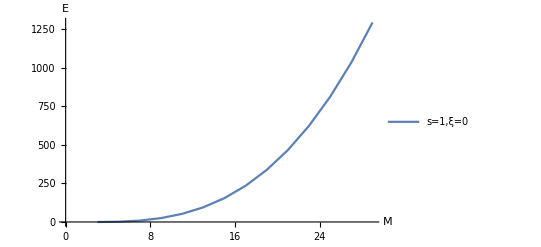

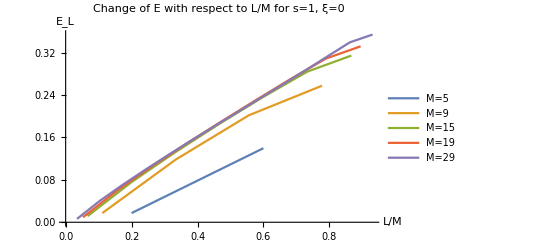

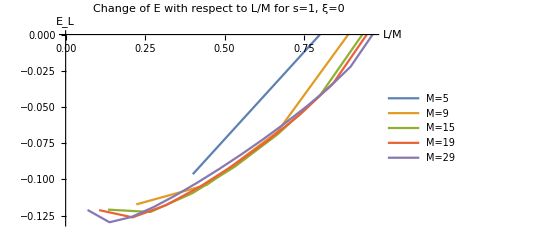

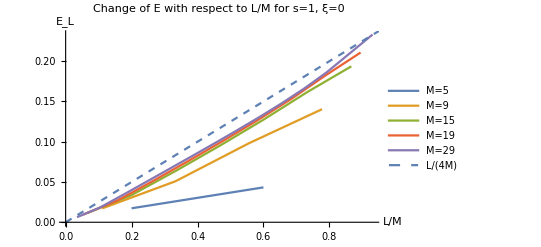

```mathematica
(* This cell demostrate how energy changes with respect to M when s=1 and xi=0.*)
PlotTotalEnergy[{1},{0}, Joined->True]
(*Export["EvM-s1xi0.pdf",%];*)
PlotEnergyCorrection[1,0,{5,9,15,19,29}, DataSet->1,NormalizeFactorM->2,Joined->True]
(*Export["SubEvM-s1xi0-a.pdf",%];*)
PlotEnergyCorrection[1,0,{5,9,15,19,29}, DataSet->2,NormalizeFactorM->2,Joined->True]
(*Export["SubEvM-s1xi0-b.pdf",%];*)
p1=PlotEnergyCorrection[1,0,{5,9,15,19,29}, DataSet->3,NormalizeFactorM->2,Joined->True];
p2=Plot[x/4,{x,0,1}, PlotStyle->Dashed, PlotLegends->{"L/(4M)"}];
Show[p1,p2]
(*Export["SubEvM-s1xi0-c.pdf",%];*)
```

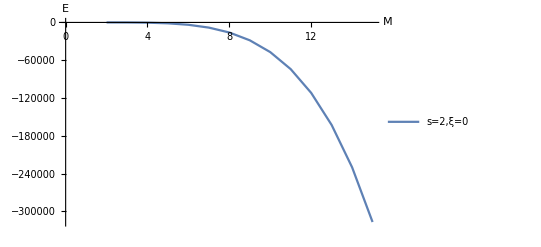

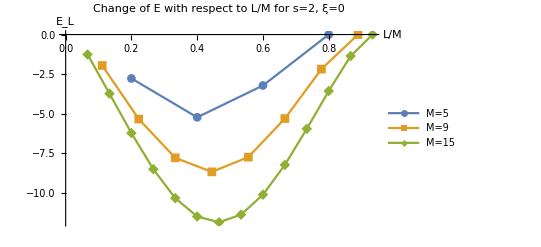

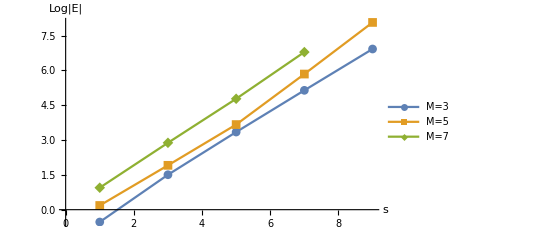

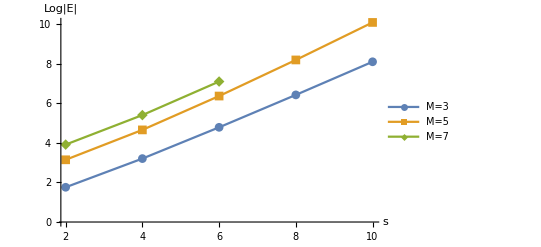

```mathematica
(* This cell investigate how E changes with respect to s. *)
PlotTotalEnergy[{2},{0}, Joined->True]
Export["EvM-s2xi0.pdf",%];
PlotEnergyCorrection[2,0,{5,9,15}, DataSet->0,NormalizeFactorM->3,Joined->True,PlotMarkers->Automatic]
Export["SubEvM-s2xi0.pdf",%];
PlotEvsS[{3,5,7},0,Joined->True,LogData->True, DataSet->1]
Export["EvS-xi0-odd.pdf",%];
PlotEvsS[{3,5,7},0,Joined->True,LogData->True, DataSet->2]
Export["EvS-xi0-even.pdf",%];
```

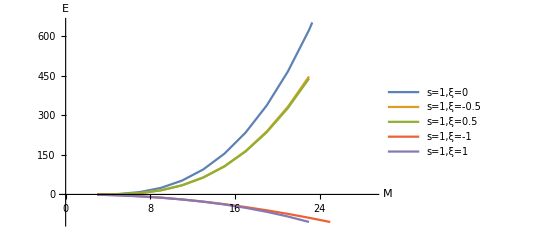

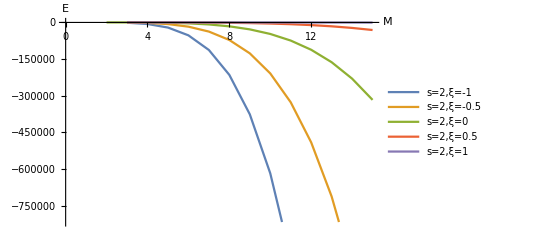

```mathematica
(* This cell investigates how E changes with respect to ξ *)
PlotTotalEnergy[{1},{0,-0.5,0.5,-1,1},Joined->True]
Export["EvM-s1-manyxi.pdf",%];
PlotTotalEnergy[{2},{-1,-0.5,0,0.5,1},Joined->True]
Export["EvM-s2-manyxi.pdf",%];
```